```mathematica
{1,2,3,4,6}/2
```

{1/2,1,3/2,2,3}

```mathematica
rvo = RandomVariate[BinomialDistribution[10,0.5],1000]/10;
```

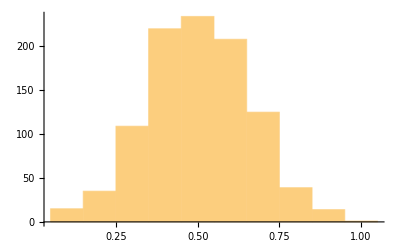

```mathematica
Histogram[rvo]
```

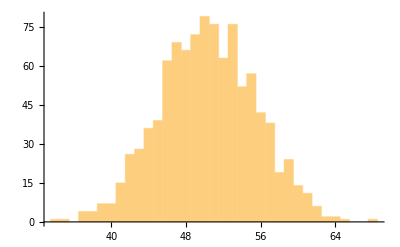

```mathematica
Histogram[RandomVariate[BinomialDistribution[100,0.5],1000]]
```

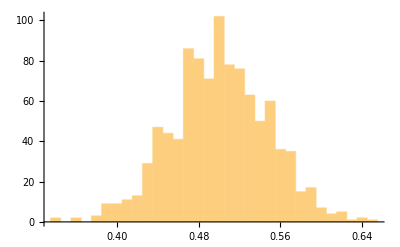

```mathematica
Histogram[RandomVariate[BinomialDistribution[100,0.5],1000]/100]
```

```mathematica
die1 = RandomVariate[DiscreteUniformDistribution[{1,6}], 10000];
```

```mathematica
die2 = RandomVariate[DiscreteUniformDistribution[{1,6}], 10000];
```

```mathematica
rvo2 = die1 + die2;
```

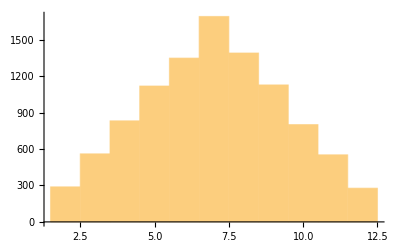

```mathematica
Histogram[rvo2]
```

```mathematica
Probability[x==2, x \[Distributed] rvo2]
```

289/10000

```mathematica
N[289/10000]
```

0.0289

```mathematica
N[Probability[x==3, x \[Distributed] rvo2]]
```

0.0561

```mathematica
N[Probability[x==5, x \[Distributed] rvo2]]
```

0.112

```mathematica
Probability[
 x + y==5, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/9

```mathematica
N[Probability[
 x + y==2, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]]
```

0.0277778

```mathematica
Probability[
 x + y==5, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/9

```mathematica
Probability[
 x + y==7, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/6

```mathematica
CDF[BernoulliDistribution[0.5],0.8]
```

0.5

```mathematica
CDF[BernoulliDistribution[0.5],{0.3, 0.8}]
```

{0.5,0.5}

```mathematica
CDF[BernoulliDistribution[p]]
```

Function[x,Piecewise[{{0, x<0}, {1-p, 0≤x<1}, {1, True}}],Listable]

```mathematica
PDF[BernoulliDistribution[p]]
```

Function[x,Piecewise[{{1-p, x==0}, {p, x==1}, {0, True}}],Listable]

```mathematica
CDF[GeometricDistribution[0.5]]
```

Function[x,Piecewise[{{1-0.5^(1+Floor[x]), x≥0}, {0, True}}],Listable]

```mathematica
PDF[GeometricDistribution[p]]
```

Function[x,Piecewise[{{(1-p)^x p, x≥0}, {0, True}}],Listable]

```mathematica
Probability[
 x ==4 && y == 3, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/36

```mathematica
Probability[
 x+y ==7, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/6

```mathematica
Probability[40.2≤x≤ 59.8,x \[Distributed] BinomialDistribution[100,0.5]]
```

0.943112

```mathematica
a = TransformedDistribution[x/100, x \[Distributed] BinomialDistribution[100, 0.5]]
```

TransformedDistribution[x/100,x\[Distributed]BinomialDistribution[100,0.5]]

```mathematica
Probability[0.402≤y≤ 0.598, y \[Distributed]a]
```

0.943112

```mathematica
N[Probability[7≤x≤ 9,x \[Distributed] NormalDistribution[10,3]]]
```

0.210786

```mathematica
Manipulate[Histogram[RandomVariate[ExponentialDistribution[x], 1000]], {x, 0.1, 0.9}]
```

```mathematica
N[Probability[x> 2,x \[Distributed] NormalDistribution[0,1]]]
```

0.0227501

```mathematica
Probability[x>1,x \[Distributed] ExponentialDistribution[λ]]
```

ⅇ^-λ

```mathematica
ProbabilityDistribution[Piecewise[{{(1/(25*x)),0<x<5},{0.4-(x/25),5≤x≤10}}], {x, -Infinity, Infinity}]
```

ProbabilityDistribution[Piecewise[{{1/(25 x), 0<x<5}, {0.4-x/25, 5≤x≤10}, {0, True}}],{x,0,∞}]

```mathematica
NumberForm[Probability[x≤3, x\[Distributed]ProbabilityDistribution[Piecewise[{{(x/25),0<x<5},{0.4-(x/25),5≤x≤10}}], {x, -Infinity, Infinity}]], 3]
```

0.18

```mathematica
Rationalize[0.18000000000000022]
```

9/50

```mathematica
Expectation[y, y\[Distributed]GeometricDistribution[p]]
```

(1-p)/p

```mathematica
Simplify[(1-p)/p]
```

-1+1/p

```mathematica
Expectation[x, x\[Distributed]GeometricDistribution[0.2]]
```

4.

```mathematica
(1-0.2)/0.2
```

4.

```mathematica
Expectation[c, x\[Distributed]BernoulliDistribution[p]]
```

c

```mathematica
Expectation[a*x+b, x\[Distributed]BernoulliDistribution[p]]
```

b+a p

```mathematica
Variance[BernoulliDistribution[p]]
```

(1-p) p

```mathematica
Variance[GeometricDistribution[p]]
```

(1-p)/p^2

```mathematica
Expectation[a*x+b, x\[Distributed]GeometricDistribution[p]]
```

(a-a p+b p)/p

```mathematica
Expectation[(2*x)+3, x\[Distributed]GeometricDistribution[p]]
```

(2+p)/p

```mathematica
2*((1-p)/p) + 3
```

3+(2 (1-p))/p

```mathematica
Simplify[3+(2 (1-p))/p]
```

(2+p)/p

```mathematica
f[x_]:=2*x
```

```mathematica
Expectation[f[x], x\[Distributed]GeometricDistribution[p]]
```

-(2 (-1+p))/p

```mathematica
Simplify[-(2 (-1+p))/p]
```

-2+2/p

```mathematica
Distro = ProbabilityDistribution[Sqrt[2]/Pi/(1 + x^4), {x, -Infinity, Infinity}];
```

```mathematica
Expectation[x, x \[Distributed]Distro]
```

0

```mathematica
Variance[Distro]
```

1

```mathematica
PDF[DiscreteUniformDistribution[{0,9}]]
```

Function[x,Piecewise[{{1/10, 0≤x≤9}, {0, True}}],Listable]

```mathematica
Expectation[x, x\[Distributed]DiscreteUniformDistribution[{0, 9}]]
```

9/2

```mathematica
uniformData = RandomChoice[{0,1,2,3,4,5,6,7,8,9}, 1000];
```

```mathematica
FindDistribution[uniformData]
```

DiscreteUniformDistribution[{0,9}]

```mathematica
N[Variance[DiscreteUniformDistribution[{0,9}]]]
```

8.25

```mathematica
Variance[DiscreteUniformDistribution[{a,b}]]
```

1/12 (-1+(1-a+b)^2)

Suppose you toss a fair coin 12 times. What is the probability that you will get 5 heads?

```mathematica
Probability[x==5, x\[Distributed]BinomialDistribution[12,0.5]]
```

0.193359

```mathematica
Total[Probability[x=={0, 1,2, 5}, x\[Distributed]BinomialDistribution[12,0.5]]]
```

0.212646

```mathematica
Variance[BinomialDistribution[n,p]]
```

n (1-p) p

```mathematica
a = RandomChoice[{0,1}, 10]
```

{1,1,1,1,1,1,0,1,0,0}

```mathematica
b = RandomChoice[{0,1},10]
```

{1,0,1,1,1,0,1,1,1,1}

```mathematica
FindDistribution[a]
```

BinomialDistribution[1,0.666667]

```mathematica
FindDistribution[b]
```

BinomialDistribution[1,0.75]

```mathematica
c = RandomChoice[{0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10},10]
```

{2,0,5,0,8,0,0,9,1,7}

```mathematica
FindDistribution[c]
```

MixtureDistribution[{0.583218,0.416782},{PoissonDistribution[0.429198],BinomialDistribution[10,0.759714]}]

```mathematica
d = {2,5,6,4,3,6,6,5,6,4}
```

{2,5,6,4,3,6,6,5,6,4}

```mathematica
e = RandomVariate[BinomialDistribution[10, 0.5],100];
```

```mathematica
FindDistributionParameters[e,BinomialDistribution[n,p],
ParameterEstimator->"MaximumLikelihood"]
```

{n→9,p→0.55}

```mathematica
FindDistributionParameters[e, BinomialDistribution[n,p]]
```

{n→9,p→0.55}

```mathematica
ProbabilityDistribution[Piecewise[{{c/(x^2),10≤x≤20},{0,Not[10≤x≤20]}}], {x, -Infinity, Infinity}]
```

ProbabilityDistribution[Piecewise[{{c/x^2, 10≤x≤20}, {0, True}}],{x,-∞,∞}]

```mathematica
PDF[ProbabilityDistribution[Piecewise[{{c/x^2,10≤x≤20}},0],{x,-∞,∞}],x]
```

Piecewise[{{c/x^2, 10≤x≤20}, {0, True}}]

```mathematica
∫Piecewise[{{c/x^2,10≤x≤20}},0]ⅆx
```

Piecewise[{{0, x≤10}, {c/10-c/x, 10<x≤20}, {c/20, True}}]

```mathematica
Solve[∫Piecewise[{{c/x^2,10≤x≤20}},0]ⅆx == 1, c]
```

{{c→ConditionalExpression[20, x>20]},{c→ConditionalExpression[(10 x)/(-10+x), 10<x<20]}}

```mathematica
First[{{c->ConditionalExpression[20,x>20]},{c->ConditionalExpression[(10 x)/(-10+x),10<x<20]}}]
```

{c→ConditionalExpression[20, x>20]}

```mathematica
PDF[ProbabilityDistribution[Piecewise[{{c/x^2,10≤x≤20}},0],{x,-∞,∞}],x]
```

Piecewise[{{c/x^2, 10≤x≤20}, {0, True}}]

```mathematica
Integrate[PDF[ProbabilityDistribution[Piecewise[{{c/x^2,10≤x≤20}},0],{x,-∞,∞}],x], {x, -Infinity, Infinity}]
```

c/20

```mathematica
Integrate[PDF[ProbabilityDistribution[Piecewise[{{20/(x^2),10≤x≤20}},0],{x,-∞,∞}],x], {x, -Infinity, Infinity}]
```

1

```mathematica
Integrate[PDF[ProbabilityDistribution[Piecewise[{{20/(x^2),10≤x≤20}},0],{x,-∞,∞}],x], {x, 10, 20}]
```

1

```mathematica
Integrate[PDF[ProbabilityDistribution[Piecewise[{{30/(x^2),10≤x≤20}},0],{x,-∞,∞}],x], {x, 10, 20}]
```

3/2

```mathematica
Plot[20/(x^2), {x, 10, 20}]
```

-Graphics-

```mathematica
Integrate[20/(x^2), {x, 10, 20}]
```

1

```mathematica
NProbability[n > 4, n \[Distributed] PoissonDistribution[4/60 10]]
```

0.000632521

```mathematica
Expectation[x, x \[Distributed]PoissonDistribution[λ]]
```

λ

```mathematica
Variance[PoissonDistribution[λ]]
```

λ

```mathematica
NProbability[x==5,x\[Distributed]PoissonDistribution[4.5]]
```

0.170827

```mathematica
NProbability[x≤5,x\[Distributed]PoissonDistribution[4.5]]
```

0.70293

```mathematica
1 - NProbability[x==5,x\[Distributed]BinomialDistribution[5, 2/3]]
```

0.868313

```mathematica
1 -
```

```mathematica
PDF[ProbabilityDistribution[k*x,{x,1,5}]]
```

Function[x,Piecewise[{{x k, 1<x<5}, {0, True}}],Listable]

```mathematica
Solve[k + 2k + 3k + 4k + 5k == 1, k]
```

{{k→1/15}}

```mathematica
PDF[ProbabilityDistribution[(1/15)*x,{x,1,5}]]
```

Function[x,Piecewise[{{x/15, 1<x<5}, {0, True}}],Listable]

```mathematica
Derivative[-1][Function[x,Piecewise[{{x/15,1<x<5}},0],Listable]]
```

Function[x,Piecewise[{{0, x≤1}, {-1/30+x^2/30, 1<x≤5}, {4/5, True}}],Listable]

```mathematica
Probability[2≤x≤4, x\[Distributed]ProbabilityDistribution[(1/15)*x,{x,1,5}]]
```

2/5

```mathematica
Total[{1, 2,3, 4,5} * (1/15)]
```

1

```mathematica
Total[({1, 2, 3,4 ,5}^2)*(1/50)]
```

11/10

```mathematica
ProbabilityDistribution[Log10[(x+1)/x],{x,1,9}]
```

ProbabilityDistribution[Log[(1+x)/x]/Log[10],{x,1,9}]

```mathematica
Expectation[x, x\[Distributed]ProbabilityDistribution[Log10[(x+1)/x],{x,1,9}]]
```

(8-81 Log[9]+80 Log[10])/Log[100]

```mathematica
N[(8-81 Log[9]+80 Log[10])/Log[100]]
```

3.09036

```mathematica
Expectation[x, x\[Distributed]GeometricDistribution[0.6]]
```

0.666667

```mathematica
Rationalize[0.6666666666666666]
```

2/3